```mathematica
Map[VertexCount[stubbornForm5[#,"graph"]]&, Select[Keys[stubbornForm5],With[{g=stubbornForm5[#,"graph"],set=stubbornForm6[#,"vertexsets"]},IsomorphicGraphQ[g,Graph[{1<->2}]]
]&]]//Tally//Sort
```

{{2,15}}

```mathematica
cycleKeys5=Select[Keys[stubbornForm5],With[{g=stubbornForm5[#,"graph"],set=stubbornForm6[#,"vertexsets"]},IsomorphicGraphQ[g,CycleGraph[VertexCount[g]]]&&VertexCount[g]≠4
]&]
```

{3195,3243,7407,7615,8859,9019,20505,20665,21909,22117,26281,26329,29537,29560,29608,29633,29768,29797,29857,30262,30334,30496,31714,31738,31954,32441,36086,36112,36166,36817,38281,49208,49210,49216,49963,51475,56011}

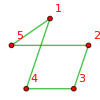
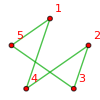
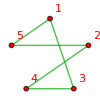
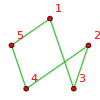
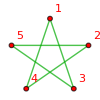
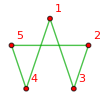
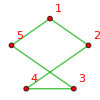
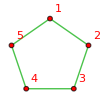
{-Graphics-{3195→v12x35x4+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,10},-Graphics-{3243→v12x34x5+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,10},-Graphics-{7407→v12x35x4+v12x3x45+v12x3x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x23x45+v1x23x4x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,10},-Graphics-{7615→v12x34x5+v12x35x4+v12x3x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,10},-Graphics-{8859→v12x34x5+v12x3x45+v12x3x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,10},-Graphics-{9019→v12x34x5+v12x35x4+v12x3x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,10},-Graphics-{20505→v13x25x4+v13x2x45+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x23x45+v1x23x4x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,10},-Graphics-{20665→v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,10},-Graphics-{21909→v13x24x5+v13x2x45+v13x2x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x3x5+v1x2x3x45+v1x2x3x4x5,10},-Graphics-{22117→v13x24x5+v13x25x4+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,10},-Graphics-{26281→v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,10},-Graphics-{26329→v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,10},-Graphics-{29537→v1x2x345,1},-Graphics-{29560→v1x25x34,1},-Graphics-{29608→v1x24x35,1},-Graphics-{29633→v1x245x3,1},-Graphics-{29768→v1x23x45,1},-Graphics-{29797→v1x235x4,1},-Graphics-{29857→v1x234x5,1},-Graphics-{30262→v15x2x34,1},-Graphics-{30334→v15x24x3,1},-Graphics-{30496→v15x23x4,1},-Graphics-{31714→v14x2x35,1},-Graphics-{31738→v14x25x3,1},-Graphics-{31954→v14x23x5,1},-Graphics-{32441→v145x2x3,1},-Graphics-{36086→v13x2x45,1},-Graphics-{36112→v13x25x4,1},-Graphics-{36166→v13x24x5,1},-Graphics-{36817→v135x2x4,1},-Graphics-{38281→v134x2x5,1},-Graphics-{49208→v12x3x45,1},-Graphics-{49210→v12x35x4,1},-Graphics-{49216→v12x34x5,1},-Graphics-{49963→v125x3x4,1},-Graphics-{51475→v124x3x5,1},-Graphics-{56011→v123x4x5,1}}

```mathematica
Table[CosyPrint5[k],{k,cycleKeys5}]
```

```mathematica
Graph[1<->2]
```

Graph[1<->2]

```mathematica
treeKeys5=Select[Keys[stubbornForm5],With[{g=stubbornForm5[#,"graph"],set=stubbornForm6[#,"vertexsets"]},TreeGraphQ[g]&&EdgeCount[g]==VertexCount[g]-1&&
VertexCount[g]≠4&&Max[ Table[VertexDegree[g,v],{v, VertexList[g]}]]<=2
]&]
```

{822,846,982,1008,1054,1056,1426,2226,2298,2434,2458,2466,2514,2824,2952,3000,3162,3168,3186,3240,3524,4222,5620,6598,6646,6672,6678,6832,6886,7034,7326,7372,7380,7398,7534,7614,7738,8436,8776,8778,8832,8856,8992,9018,9148,9854,10552,11244,11950,12650,14044,15454,16160,16864,18274,19720,19722,19768,19776,19930,19936,20060,20422,20424,20496,20502,20656,20664,20812,21510,21874,21882,21900,21906,22114,22116,22318,23072,23770,24414,25168,25868,26248,26254,26272,26280,26326,26328,26852,27610,28308,29128,29186,29232,29328,29378,29648,29706,29826,29888,29938,30082,30406,30586,31224,31444,31492,31924,31984,32198,32684,33158,33916,34620,35434,35978,36030,36138,36194,36736,36898,37548,38254,38308,39014,40144,41650,42404,43156,44662,46184,46942,47694,48460,49196,49200,49212,49220,49954,49972,50718,51472,51478,52232,53734,55252,56010,56012,56770,58288,59048}

```mathematica
Length[treeKeys5]
```

151

```mathematica
Flatten[Table[ListofVars[stubbornForm5[ k,"colofour"]],{k,treeKeys5}]]//DeleteDuplicates//Length
```

40

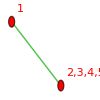
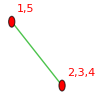
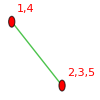
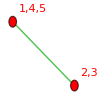
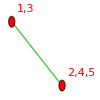
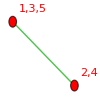
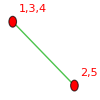
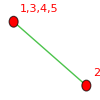
{-Graphics-{29888→v1x2345,1/2},-Graphics-{30586→v15x234,1/2},-Graphics-{31984→v14x235,1/2},-Graphics-{32684→v145x23,1/2},-Graphics-{36194→v13x245,1/2},-Graphics-{36898→v135x24,1/2},-Graphics-{38308→v134x25,1/2},-Graphics-{39014→v1345x2,1/2},-Graphics-{49220→v12x345,1/2},-Graphics-{49972→v125x34,1/2},-Graphics-{51478→v124x35,1/2},-Graphics-{52232→v1245x3,1/2},-Graphics-{56012→v123x45,1/2},-Graphics-{56770→v1235x4,1/2},-Graphics-{58288→v1234x5,1/2}}

```mathematica
Table[CosyPrint5[k],{k,treeKeys5}]
```